## Cellular automata

A rule is represented by a number.

```mathematica
pl[a_]:=ArrayPlot[
a,
ImageSize->Length[a⟦1⟧]*10,
Mesh->All,
MeshStyle->Directive[Thickness[0.005],Gray]
]

showRule[n_]:=MatrixForm[
{
Table[i-1,{i,8,1,-1}],
Table[pl[{PadLeft[IntegerDigits[i-1,2],3]}],{i,8,1,-1}],Table["↓",{i,8}],
Map[pl,List /@ List /@ IntegerDigits[n,2]~PadLeft~8],
IntegerDigits[n,2]~PadLeft~8
}
,TableHeadings->{{"bit number =","","","the rule is coded as",n},None},
TableAlignments->Center
]

showRule[90]
```

(bit number = | 7 | 6 | 5 | 4 | 3 | 2 | 1 | 0
 | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
 | ↓ | ↓ | ↓ | ↓ | ↓ | ↓ | ↓ | ↓
the rule is coded as | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
90 | 0 | 1 | 0 | 1 | 1 | 0 | 1 | 0)

#### code

```mathematica
showMatrix[aa_,imageSize_]:=ArrayPlot[aa,Mesh->None,MeshStyle->Directive[Thickness[0.001],LightGray],ImageSize->imageSize];

rule[n_]:=IntegerDigits[n,2]~PadLeft~8;
newValue[r_,a_,i_]:= r⟦FromDigits[{a⟦i-1⟧,a⟦i⟧,a⟦i+1⟧},2] +1⟧;

newRow[r_,aa_,nCols_]:=Join[{0}, Table[newValue[r,aa⟦Length[aa]⟧,i],{i,2,nCols-1}],{0}];

buildMatrix1[nRows_,nCols_,rulNum_]:= Module[{aa,a,r},
aa={};
r =rule[rulNum]; 
a=Table[0,{i,1,nCols}]; a⟦Quotient[nCols,2]+1⟧=1; 
aa=Append[aa,a];
Do[  aa= Append[aa,newRow[r,aa,nCols]]; ,  {nRows-1}  ];
Return[aa];
]


(* Second version. Prebuit array. No appends. For loop *)
buildMatrix2[nRows_,nCols_,rulNum_]:= Module[{aa,r},
aa=Table[0,{i,1,nRows},{j,1,nCols}]; aa⟦1⟧⟦Quotient[nCols,2]+1⟧=1;
r =rule[rulNum]; 

For[ir=2,ir<=nRows, ir++,
For[ic=2,ic<nCols, ic++,
aa⟦ir⟧⟦ic⟧=newValue[r,aa⟦ir-1⟧,ic]; 
]
];

aa
]

(* Second version. Prebuilt array. No appends. Do loop.*)
buildMatrix3[nRows_,nCols_,rulNum_]:= Module[{aa,r},
aa=Table[0,{i,1,nRows},{j,1,nCols}]; aa⟦1⟧⟦Quotient[nCols,2]+1⟧=1;
r =rule[rulNum]; 
Do[
aa⟦ir⟧⟦ic⟧=newValue[r,aa⟦ir-1⟧,ic];
,{ir,2,nRows},{ic,2,nCols-1}
];
aa
]


(*buildMatrix4=Compile[{{nRows,_Integer},{nCols,_Integer},{rulNum,_Integer}},buildMatrix3[nRows_,nCols_,rulNum_]];*)

Manipulate[
showMatrix[buildMatrix2[Quotient[cols,2],cols,ruleNumber ],600]
,{{ruleNumber,90,"Rule N"},0,255,1},{{cols,100},1,500,10}
]
```

```mathematica
(*FrontEndExecute[FrontEndToken["DeleteGeneratedCells"]];*)
DynamicModule[
{NC=100,RN=90},
Slider[Dynamic[NC],{1,500,1},ImageSize->300,Appearance->"Labeled"]Slider[Dynamic[RN],{0,255,1},ImageSize->300,Appearance->"Labeled"]
(*Dynamic[ showMatrix[buildMatrix2[Quotient[NC,2],NC,RN ],600],None]*)
]
```

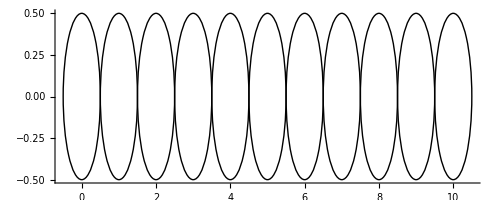

```mathematica
Graphics[Table[Circle[{i,0},0.5],{i,0,10}],Axes->True]
```

```mathematica
MapIndexed
```